# Plot Example of Full Model

```mathematica
Clear["Global`*"]
```

```mathematica
dH = eh*Vhp*H*P - th*H - Wnh*H;

dP = Vpn*P*Iorg - tp*P - Vhp*H*P ;

dM = Vmd*M*Dn - Vfm*Dv*M -tm*M- Wnm*M + Vmn*M*Iorg;

dDv = ef*(Vfd*Dv*Dn + Vfm*Dv*M) -tf*Dv - Wnf*Dv;

dDn = tm*M+ tf*Dv + tp*P +th*H -Vfd*Dv*Dn - Vmd*M*Dn -l*Dn + (1-eh)*Vhp*H*P + (1-ef)*(Vfd*Dv*Dn + Vfm*Dv*M);

dDc = μ*tm*M+ ϕ*tf*Dv + ω*tp*P +η*th*H -Vfd*Dv*Dc - Vmd*M*Dc-l*Dc + ω*(1-eh)*Vhp*H*P+ (1-ef)*(Vfd*Dv*Dc+  μ*Vfm*Dv*M);

dIorg = IN - q*Iorg  -Vpn*P*Iorg + Wnm*M +Wnf*Dv +Wnh*H - Vmn*M*Iorg;

dHc = eh*ω*Vhp*H*P - η*th*H - η*Wch*H;

dPc = ω*Vpn*P*Iorg- ω*tp*P - ω*Vhp*H*P ;

dMc = Vmd*M*Dc - μ*Vfm*Dv*M -μ*tm*M- μ*Wcm*M;

dDvc = ef*(Vfd*Dv*Dc + μ*Vfm*Dv*M) -ϕ*tf*Dv -ϕ*Wcf*Dv;
```

```mathematica
Wnj = {{exm, exf, exh},{Dn Vmd+Iorg Vmn+rm-(Dc Vmd)/μ, exf, exh},{Dn Vmd+Iorg Vmn+rm-(Dc Vmd)/μ,exf,((η-ω)/η)*eh*Vhp*P+rh},{Dn Vmd+Iorg Vmn+rm-(Dc Vmd)/μ,Dn ef Vfd+ef M Vfm+rf-(Dc ef Vfd)/ϕ-(ef M Vfm μ)/ϕ,exh},{Dn Vmd+Iorg Vmn+rm-(Dc Vmd)/μ,Dn ef Vfd+ef M Vfm+rf-(Dc ef Vfd)/ϕ-(ef M Vfm μ)/ϕ,((η-ω)/η)*eh*Vhp*P+rh},{exm,exf,((η-ω)/η)*eh*Vhp*P+rh},{exm,Dn ef Vfd+ef M Vfm+rf-(Dc ef Vfd)/ϕ-(ef M Vfm μ)/ϕ,exh},{exm,Dn ef Vfd+ef M Vfm+rf-(Dc ef Vfd)/ϕ-(ef M Vfm μ)/ϕ,((η-ω)/η)*eh*Vhp*P+rh}};

Wcj = {{-Dn Vmd-Iorg Vmn+exm+(Dc Vmd)/μ, exf+(Dn Vfd ef(Dc/Dn-ϕ)+M Vfm ef(μ-ϕ))/ϕ, (ω-η)*Vhp*P*eh/η + exh},{rm, exf+(Dn Vfd ef(Dc/Dn-ϕ)+M Vfm ef(μ-ϕ))/ϕ, (ω-η)*Vhp*P*eh/η + exh},{rm,exf+(Dn Vfd ef(Dc/Dn-ϕ)+M Vfm ef(μ-ϕ))/ϕ,rh},{rm, rf,(ω-η)*Vhp*P*eh/η + exh},{rm, rf,rh},{-Dn Vmd-Iorg Vmn+exm+(Dc Vmd)/μ,exf+(Dn Vfd ef(Dc/Dn-ϕ)+M Vfm ef(μ-ϕ))/ϕ,rh},{-Dn Vmd-Iorg Vmn+exm+(Dc Vmd)/μ, rf,(ω-η)*Vhp*P*eh/η + exh},{-Dn Vmd-Iorg Vmn+exm+(Dc Vmd)/μ, rf,rh}};
```

```mathematica
dH5 = eh*Vhp*H5*P5 - th*H5 - Wnh5*H5;

dP5 = Vpn*P5*Iorg5 - tp*P5 - Vhp*H5*P5 ;

dM5 = Vmd*M5*Dn5 - Vfm*Dv5*M5 -tm*M5- Wnm5*M5+ Vmn*M5*Iorg5;

dDv5=  ef*(Vfd*Dv5*Dn5 + Vfm*Dv5*M5) -tf*Dv5 - Wnf5*Dv5;

dDn5 = tm*M5+ tf*Dv5 + tp*P5 +th*H5 -Vfd*Dv5*Dn5 - Vmd*M5*Dn5 -l*Dn5+ (1-eh)*Vhp*H5*P5 + (1-ef)*(Vfd*Dv5*Dn5 + Vfm*Dv5*M5);

dDc5 = μ*tm*M5+ ϕ*tf*Dv5 + ω*tp*P5 +η*th*H5 -Vfd*Dv5*Dc5 - Vmd*M5*Dc5-l*Dc5 + ω*(1-eh)*Vhp*H5*P5+ (1-ef)*(Vfd*Dv5*Dc5+  μ*Vfm*Dv5*M5);

dIorg5= IN - q*Iorg5  -Vpn*P5*Iorg5 + Wnm5*M5 +Wnf5*Dv5 +Wnh5*H5- Vmn*M5*Iorg5;

Wnj5 = {{exm, exf, exh},{Dn5 Vmd+Iorg5 Vmn+rm-(Dc5 Vmd)/μ, exf, exh},{Dn5 Vmd+Iorg5 Vmn+rm-(Dc5 Vmd)/μ,exf,((η-ω)/η)*eh*Vhp*P5+rh},{Dn5 Vmd+Iorg5 Vmn+rm-(Dc5 Vmd)/μ,Dn5 ef Vfd+ef M5 Vfm+rf-(Dc5 ef Vfd)/ϕ-(ef M5 Vfm μ)/ϕ,exh},{Dn5 Vmd+Iorg5 Vmn+rm-(Dc5 Vmd)/μ,Dn5 ef Vfd+ef M5 Vfm+rf-(Dc5 ef Vfd)/ϕ-(ef M5 Vfm μ)/ϕ,((η-ω)/η)*eh*Vhp*P5+rh},{exm,exf,((η-ω)/η)*eh*Vhp*P5+rh},{exm,Dn5 ef Vfd+ef M5 Vfm+rf-(Dc5 ef Vfd)/ϕ-(ef M5 Vfm μ)/ϕ,exh},{exm,Dn5 ef Vfd+ef M5 Vfm+rf-(Dc5 ef Vfd)/ϕ-(ef M5 Vfm μ)/ϕ,((η-ω)/η)*eh*Vhp*P5+rh}};

Wcj5 = {{-Dn5 Vmd-Iorg5 Vmn+exm+(Dc5 Vmd)/μ, exf+(Dn5 Vfd ef(Dc5/Dn5-ϕ)+M5 Vfm ef(μ-ϕ))/ϕ, (ω-η)*Vhp*P5*eh/η + exh},{rm, exf+(Dn5 Vfd ef(Dc5/Dn5-ϕ)+M5 Vfm ef(μ-ϕ))/ϕ, (ω-η)*Vhp*P5*eh/η + exh},{rm,exf+(Dn5 Vfd ef(Dc5/Dn5-ϕ)+M5 Vfm ef(μ-ϕ))/ϕ,rh},{rm, rf,(ω-η)*Vhp*P5*eh/η + exh},{rm, rf,rh},{-Dn5 Vmd-Iorg5 Vmn+exm+(Dc5 Vmd)/μ,exf+(Dn5 Vfd ef(Dc5/Dn5-ϕ)+M5 Vfm ef(μ-ϕ))/ϕ,rh},{-Dn5 Vmd-Iorg5 Vmn+exm+(Dc5 Vmd)/μ, rf,(ω-η)*Vhp*P5*eh/η + exh},{-Dn5 Vmd-Iorg5 Vmn+exm+(Dc5 Vmd)/μ, rf,rh}};

J =Table[

{Wnm5,Wnf5,Wnh5} = Wnj5[[sc,All]];
{Wcm5,Wcf5,Wch5} = Wcj5[[sc,All]];
JacobianMatrix[fns_List, vars_List]:=Outer[D,fns,vars];
JacobianMatrix[{dH5,dP5,dM5,dDv5,dDn5,dDc5,dIorg5},{H5,P5,M5,Dv5,Dn5,Dc5, Iorg5}]

,{sc,1,8}];
```

```mathematica
solex2 =Table[

{Wnm,Wnf,Wnh} = Wnj[[sc,All]];
{Wcm,Wcf,Wch} = Wcj[[sc,All]];

solex = Solve[{dP==0, dM==0, dDn==0,dIorg==0, dH==0, dDv==0},{P,M,Dn,Iorg, H, Dv}]/. Rule-> List;
Select[solex[[All,All,2]], Not[MemberQ[#,0]]&]
,{sc,1,8}];
```

```mathematica
solex2B =Table[

{Wnm,Wnf,Wnh} = Wnj[[sc,All]];
{Wcm,Wcf,Wch} = Wcj[[sc,All]];

solex = Solve[{dP==0, dM==0, dDn==0,dDc==0,dIorg==0, dH==0, dDv==0},{P,M,Dn,Dc,Iorg, H, Dv}]/. Rule-> List;
Select[solex[[All,All,2]], Not[MemberQ[#,0]]&]
,{sc,{1,4,5}}];
```

```mathematica
{IN,q,l,Vpn,Vhp, Vfd, Vfm, Vmd, Vmn,rm,rh,rf,exm,exf,exh,tp,th, tm, tf,η,ω,μ,ϕ,ef,eh}={59.770553581252784,1.0463073402690526,23.791589294054532,55.69291599467229,93.94236487158977,44.550998625843704,45.36420071348638,61.77294384412983,8.702115141916948,63.84398597496488,84.25533781733236,67.39845111426445,32.5608384640486,81.58679306242306,71.88606788341141,69.07032708742824,80.12681723172409,8.55607178354984,95.98836423541348,8.601913778321109,10.3329174578422,8.571608152120305,8.935926674853052,0.33092005393088475,0.6780087589998158}
```

# Omega

```mathematica
output=Table[
partone = Table[
{Wnm,Wnf,Wnh} = Wnj[[sc,All]];
{Wcm,Wcf,Wch} = Wcj[[sc,All]];

checkB = {};
checkA =Solve[{P==solex2[[sc]][[1,1]], M==solex2[[sc]][[1,2]],Dn==solex2[[sc]][[1,3]],Iorg==solex2[[sc]][[1,4]], H==solex2[[sc]][[1,5]], Dv==solex2[[sc]][[1,6]],dDc==0},{P,M,Dn,Dc,Iorg, H, Dv}]/. Rule-> List;
If[Dimensions[solex2[[sc]]][[1]]==2,
checkB =Solve[{P==solex2[[sc]][[2,1]], M==solex2[[sc]][[2,2]],Dn==solex2[[sc]][[2,3]],Iorg==solex2[[sc]][[2,4]], H==solex2[[sc]][[2,5]], Dv==solex2[[sc]][[2,6]],dDc==0},{P,M,Dn,Dc,Iorg, H, Dv}]/. Rule-> List
];
 checkcheck = Select[Flatten[{checkA[[All,All,2]],checkB[[All,All,2]]},1],Count[#,_Complex]==0&&Count[#,_?Positive]==7&];

checkcheckout = ConstantArray[NA,12];

If[Dimensions[checkcheck][[1]]==1,

{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}=Flatten[checkcheck];
{Wnm5,Wnf5,Wnh5} = Wnj5[[sc,All]];
{Wcm5,Wcf5,Wch5} = Wcj5[[sc,All]];
rmax=Max[Re[Eigenvalues[J[[sc,All,All]]]]];
phck=Max[{eh*ω*Vhp*P5/(Wch5*η), ef*(Vfd*Dc5+μ*Vfm*M5)/(ϕ*Wcf5)}];

If[Total[Boole[Positive[{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}]]]==7&&rmax<0&&phck<19.4&&Wnf5>0&&Wnh5>0&&Wnm5>0&&Wcf5>0&&Wch5>0&&Wcm5>0,checkcheckout={P5,M5,Dn5,Dc5,Iorg5,H5,Dv5,Wnh5,Wnf5,Wnm5, Vpn*P5*Iorg5, Vmd*Dn5*M5}];

];

checkcheckout

,{sc,{2,3,6,7,8}}];

selJ = {1,4,5};

parttwo = Table[
checkAa =solex2B[[sc2,1,All]];
checkBb=solex2B[[sc2,2,All]];
 checkcheck = Select[{checkAa,checkBb},Count[#,_Complex]==0&&Count[#,_?Positive]==7&];

checkcheckout = ConstantArray[NA,12];

If[Dimensions[checkcheck][[1]]≥ 1,

{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}=Flatten[checkcheck[[1]]];
{Wnm5,Wnf5,Wnh5} = Wnj5[[selJ[[sc2]],All]];
{Wcm5,Wcf5,Wch5} = Wcj5[[selJ[[sc2]],All]];
rmax=Max[Re[Eigenvalues[J[[selJ[[sc2]],All,All]]]]];
phck=Max[{eh*ω*Vhp*P5/(Wch5*η), ef*(Vfd*Dc5+μ*Vfm*M5)/(ϕ*Wcf5)}];

If[Total[Boole[Positive[{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}]]]==7&&rmax<0&&phck<19.4&&Wnf5>0&&Wnh5>0&&Wnm5>0&&Wcf5>0&&Wch5>0&&Wcm5>0,checkcheckout={P5,M5,Dn5,Dc5,Iorg5,H5,Dv5,Wnh5,Wnf5,Wnm5, Vpn*P5*Iorg5, Vmd*Dn5*M5}];

];

checkcheckout

, {sc2,1,3}];

{parttwo[[1,All]],partone[[1,All]],partone[[2,All]],parttwo[[2,All]],parttwo[[3,All]],partone[[3,All]],partone[[4,All]],partone[[5,All]]},
{ω,8,50}];
```

```mathematica
output2=output;
```

```mathematica
output2[[1;;2,{1,2,4,5,6,7,8},All]]=NA;
output2[[3;;22,{1,3,4,5,6,7,8},All]]=NA;
output2[[23;;43,{2,3,4,5,6,7,8},All]]=NA;
```

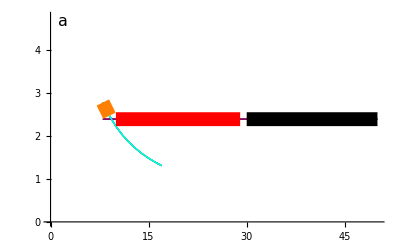
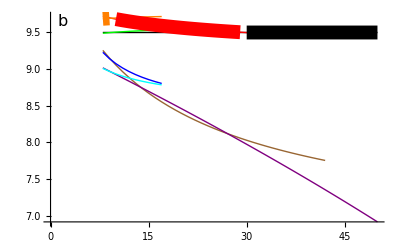
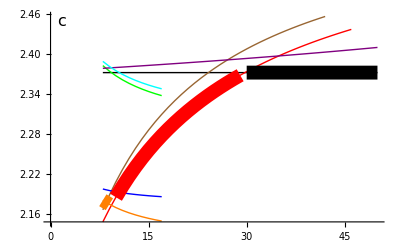
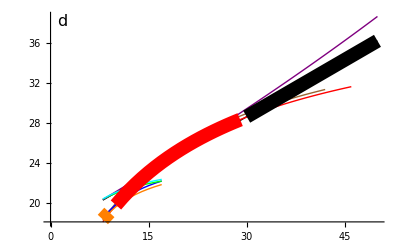
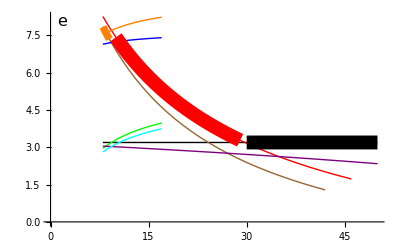
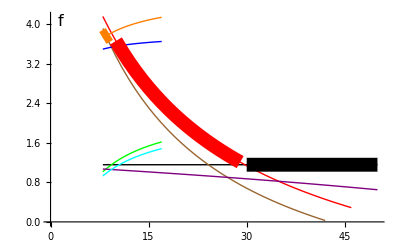
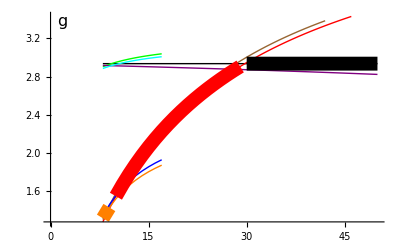
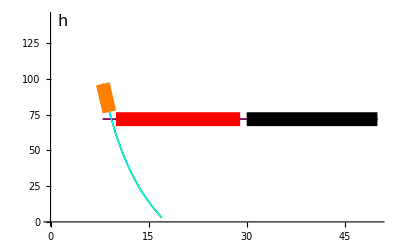
-Graphics-Plant ("P"_"N") | -Graphics-Microbes ("M"_"N") | -Graphics-Detritus N ("D"_"N")
-Graphics-Detritus C ("D"_"C") | -Graphics-Inorganic N (N) | -Graphics-Herbivore ("H"_"N")
-Graphics-Microbi-detritivore ("F"_"N") | -Graphics-H Excretion ("W"_"NH") | -Graphics-F Excretion ("W"_"NF")
-Graphics-M Excretion ("W"_"NM")Plant C:N (ω) | -Graphics-Primary ProductionPlant C:N (ω) | -Graphics-DecompositionPlant C:N (ω)

```mathematica
labeller = {"Plant ("<>ToString[Subscript["P","N"],StandardForm]<>")","Microbes ("<>ToString[Subscript["M","N"],StandardForm]<>")","Detritus N ("<>ToString[Subscript["D","N"],StandardForm]<>")","Detritus C ("<>ToString[Subscript["D","C"],StandardForm]<>")","Inorganic N (N)","Herbivore ("<>ToString[Subscript["H","N"],StandardForm]<>")","Microbi-detritivore ("<>ToString[Subscript["F","N"],StandardForm]<>")","H Excretion ("<>ToString[Subscript["W","NH"],StandardForm]<>")","F Excretion ("<>ToString[Subscript["W","NF"],StandardForm]<>")","M Excretion ("<>ToString[Subscript["W","NM"],StandardForm]<>")","Primary Production", "Decomposition"};

labeller2 = {"","","","","","","","","","Plant C:N (ω)","Plant C:N (ω)","Plant C:N (ω)"};

labeller3 = {"a", "b","c","d","e","f","g","h","i","j","k","l"};

graphicOMEGA=Grid[Partition[Table[Labeled[ListPlot[Partition[Partition[Riffle[Flatten[ConstantArray[Table[i,{i,8,50}],16]],Flatten[{Transpose[output[[All,All,sel]]],Transpose[output2[[All,All,sel]]]}]],2],43],Joined->True,
PlotStyle->{{Black},{Red}, {Orange}, {Brown}, {Blue},{Green},{Purple},{Cyan},{Thickness[0.025],Black},{Thickness[0.025],Red}, {Thickness[0.025],Orange}, {Thickness[0.025],Brown}, {Thickness[0.025],Blue},{Thickness[0.025],Green},{Thickness[0.025],Purple},{Thickness[0.025],Cyan}},Epilog->Inset[Style[labeller3[[sel]],16],Offset[{0,0},Scaled[{0.04,0.99}]],{Left,Top}]],{labeller[[sel]],labeller2[[sel]]},{Left,Bottom},RotateLabel->True, LabelStyle->{FontFamily->"Times"}],{sel,1,12}],3],Spacings->{0,-6}]
```

```mathematica
Export["AppendixS5_FigureS2.pdf",graphicOMEGA,"PDF", ImageSize->1000]
```

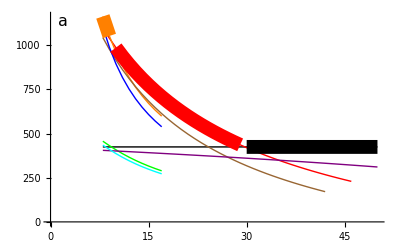
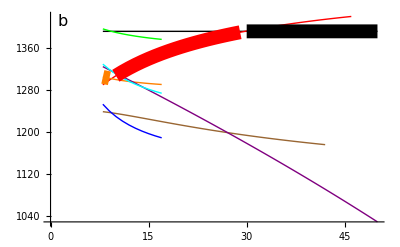
-Graphics-Primary Production
-Graphics-DecompositionPlant C:N (ω)

```mathematica
labeller2 = {"","","","","","","","Plant C:N (ω)","","Plant C:N (ω)","",""};
labeller2 = {"","","","","","","","","","","","Plant C:N (ω)"};
labeller3 = {"a", "b","c","d","e","f","g","c","i","d","a","b"};
graphicOMEGA2=Grid[Partition[Table[Labeled[ListPlot[Partition[Partition[Riffle[Flatten[ConstantArray[Table[i,{i,8,50}],16]],Flatten[{Transpose[output[[All,All,sel]]],Transpose[output2[[All,All,sel]]]}]],2],43],Joined->True,
PlotStyle->{{Black},{Red}, {Orange}, {Brown}, {Blue},{Green},{Purple},{Cyan},{Thickness[0.025],Black},{Thickness[0.025],Red}, {Thickness[0.025],Orange}, {Thickness[0.025],Brown}, {Thickness[0.025],Blue},{Thickness[0.025],Green},{Thickness[0.025],Purple},{Thickness[0.025],Cyan}},Epilog->Inset[Style[labeller3[[sel]],16],Offset[{0,0},Scaled[{0.04,0.99}]],{Left,Top}]],{labeller[[sel]],labeller2[[sel]]},{Left,Bottom},RotateLabel->True, LabelStyle->{FontFamily->"Times"}],{sel,{11,12(*,8,10*)}}],1],Spacings->{0,0}]
```

```mathematica
Export["Figure3.pdf",graphicOMEGA2,"PDF", ImageSize->1000];
```

# Mu

```mathematica
output=Table[
partone = Table[
{Wnm,Wnf,Wnh} = Wnj[[sc,All]];
{Wcm,Wcf,Wch} = Wcj[[sc,All]];

checkB = {};
checkA =Solve[{P==solex2[[sc]][[1,1]], M==solex2[[sc]][[1,2]],Dn==solex2[[sc]][[1,3]],Iorg==solex2[[sc]][[1,4]], H==solex2[[sc]][[1,5]], Dv==solex2[[sc]][[1,6]],dDc==0},{P,M,Dn,Dc,Iorg, H, Dv}]/. Rule-> List;
If[Dimensions[solex2[[sc]]][[1]]==2,
checkB =Solve[{P==solex2[[sc]][[2,1]], M==solex2[[sc]][[2,2]],Dn==solex2[[sc]][[2,3]],Iorg==solex2[[sc]][[2,4]], H==solex2[[sc]][[2,5]], Dv==solex2[[sc]][[2,6]],dDc==0},{P,M,Dn,Dc,Iorg, H, Dv}]/. Rule-> List
];
 checkcheck = Select[Flatten[{checkA[[All,All,2]],checkB[[All,All,2]]},1],Count[#,_Complex]==0&&Count[#,_?Positive]==7&];

checkcheckout = ConstantArray[NA,12];

If[Dimensions[checkcheck][[1]]==1,

{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}=Flatten[checkcheck];
{Wnm5,Wnf5,Wnh5} = Wnj5[[sc,All]];
{Wcm5,Wcf5,Wch5} = Wcj5[[sc,All]];
rmax=Max[Re[Eigenvalues[J[[sc,All,All]]]]];
phck=Max[{eh*ω*Vhp*P5/(Wch5*η), ef*(Vfd*Dc5+μ*Vfm*M5)/(ϕ*Wcf5)}];

If[Total[Boole[Positive[{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}]]]==7&&rmax<0&&phck<19.4&&Wnf5>0&&Wnh5>0&&Wnm5>0&&Wcf5>0&&Wch5>0&&Wcm5>0,checkcheckout={P5,M5,Dn5,Dc5,Iorg5,H5,Dv5,Wnh5,Wnf5,Wnm5, Vpn*P5*Iorg5, Vmd*Dn5*M5}];

];

checkcheckout

,{sc,{2,3,6,7,8}}];

selJ = {1,4,5};

parttwo = Table[
checkAa =solex2B[[sc2,1,All]];
checkBb=solex2B[[sc2,2,All]];
 checkcheck = Select[{checkAa,checkBb},Count[#,_Complex]==0&&Count[#,_?Positive]==7&];

checkcheckout = ConstantArray[NA,12];

If[Dimensions[checkcheck][[1]]≥ 1,

{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}=Flatten[checkcheck[[1]]];
{Wnm5,Wnf5,Wnh5} = Wnj5[[selJ[[sc2]],All]];
{Wcm5,Wcf5,Wch5} = Wcj5[[selJ[[sc2]],All]];
rmax=Max[Re[Eigenvalues[J[[selJ[[sc2]],All,All]]]]];
phck=Max[{eh*ω*Vhp*P5/(Wch5*η), ef*(Vfd*Dc5+μ*Vfm*M5)/(ϕ*Wcf5)}];

If[Total[Boole[Positive[{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}]]]==7&&rmax<0&&phck<19.4&&Wnf5>0&&Wnh5>0&&Wnm5>0&&Wcf5>0&&Wch5>0&&Wcm5>0,checkcheckout={P5,M5,Dn5,Dc5,Iorg5,H5,Dv5,Wnh5,Wnf5,Wnm5, Vpn*P5*Iorg5, Vmd*Dn5*M5}];

];

checkcheckout

, {sc2,1,3}];

{parttwo[[1,All]],partone[[1,All]],partone[[2,All]],parttwo[[2,All]],parttwo[[3,All]],partone[[3,All]],partone[[4,All]],partone[[5,All]]},
{μ,4,16}];
```

```mathematica
output2=output;
```

```mathematica
output2[[1;;5,{1,2,3,5,6,7,8},All]]=NA;
output2[[6;;13,{1,3,4,5,6,7,8},All]]=NA;
```

```mathematica
Dimensions[output]
```

{13,8,12}

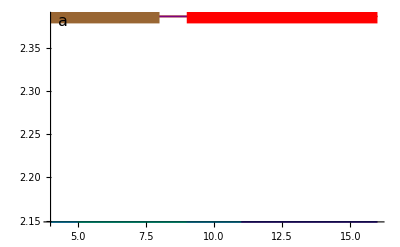
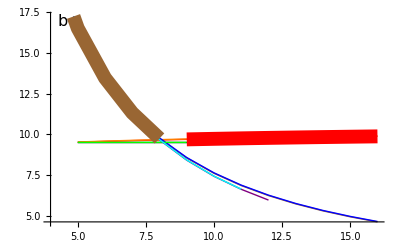
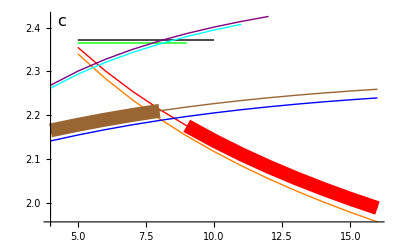
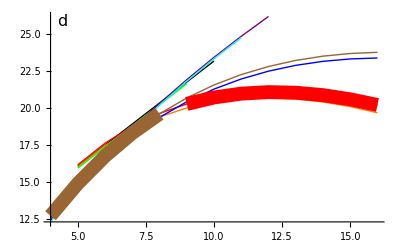
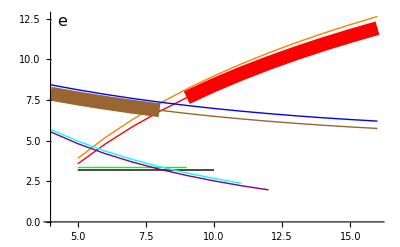
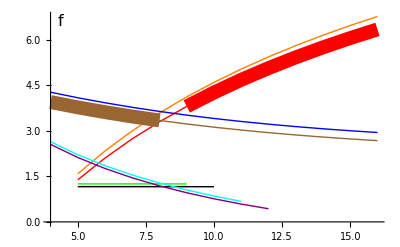
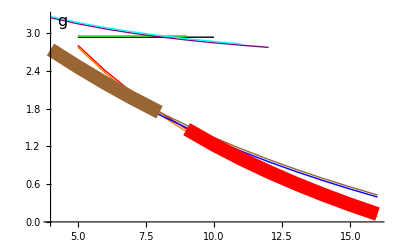
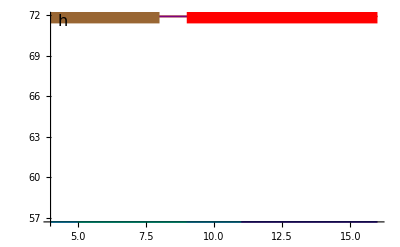
-Graphics-Plant ("P"_"N") | -Graphics-Microbes ("M"_"N") | -Graphics-Detritus N ("D"_"N")
-Graphics-Detritus C ("D"_"C") | -Graphics-Inorganic N (N) | -Graphics-Herbivore ("H"_"N")
-Graphics-Microbi-detritivore ("F"_"N") | -Graphics-H Excretion ("W"_"NH") | -Graphics-F Excretion ("W"_"NF")
-Graphics-M Excretion ("W"_"NM")Microbial C:N (μ) | -Graphics-Primary ProductionMicrobial C:N (μ) | -Graphics-DecompositionMicrobial C:N (μ)

```mathematica
labeller = {"Plant ("<>ToString[Subscript["P","N"],StandardForm]<>")","Microbes ("<>ToString[Subscript["M","N"],StandardForm]<>")","Detritus N ("<>ToString[Subscript["D","N"],StandardForm]<>")","Detritus C ("<>ToString[Subscript["D","C"],StandardForm]<>")","Inorganic N (N)","Herbivore ("<>ToString[Subscript["H","N"],StandardForm]<>")","Microbi-detritivore ("<>ToString[Subscript["F","N"],StandardForm]<>")","H Excretion ("<>ToString[Subscript["W","NH"],StandardForm]<>")","F Excretion ("<>ToString[Subscript["W","NF"],StandardForm]<>")","M Excretion ("<>ToString[Subscript["W","NM"],StandardForm]<>")","Primary Production", "Decomposition"};

labeller2 = {"","","","","","","","","","Microbial C:N (μ)","Microbial C:N (μ)","Microbial C:N (μ)"};

labeller3 = {"a", "b","c","d","e","f","g","h","i","j","k","l"};

graphicMU=Grid[Partition[Table[Labeled[ListPlot[Partition[Partition[Riffle[Flatten[ConstantArray[Table[i,{i,4,16}],16]],Flatten[{Transpose[output[[All,All,sel]]],Transpose[output2[[All,All,sel]]]}]],2],13],Joined->True,
PlotStyle->{{Black},{Red}, {Orange}, {Brown}, {Blue},{Green},{Purple},{Cyan},{Thickness[0.025],Black},{Thickness[0.025],Red}, {Thickness[0.025],Orange}, {Thickness[0.025],Brown}, {Thickness[0.025],Blue},{Thickness[0.025],Green},{Thickness[0.025],Purple},{Thickness[0.025],Cyan}},Epilog->Inset[Style[labeller3[[sel]],16],Offset[{0,0},Scaled[{0.04,0.99}]],{Left,Top}]],{labeller[[sel]],labeller2[[sel]]},{Left,Bottom},RotateLabel->True, LabelStyle->{FontFamily->"Times"}],{sel,1,12}],3],Spacings->{0,-6}]
```

```mathematica
Export["AppendixS5_FigureS3.pdf",graphicMU,"PDF", ImageSize->1000]
```

# IN

```mathematica
output=Table[
partone = Table[
{Wnm,Wnf,Wnh} = Wnj[[sc,All]];
{Wcm,Wcf,Wch} = Wcj[[sc,All]];

checkB = {};
checkA =Solve[{P==solex2[[sc]][[1,1]], M==solex2[[sc]][[1,2]],Dn==solex2[[sc]][[1,3]],Iorg==solex2[[sc]][[1,4]], H==solex2[[sc]][[1,5]], Dv==solex2[[sc]][[1,6]],dDc==0},{P,M,Dn,Dc,Iorg, H, Dv}]/. Rule-> List;
If[Dimensions[solex2[[sc]]][[1]]==2,
checkB =Solve[{P==solex2[[sc]][[2,1]], M==solex2[[sc]][[2,2]],Dn==solex2[[sc]][[2,3]],Iorg==solex2[[sc]][[2,4]], H==solex2[[sc]][[2,5]], Dv==solex2[[sc]][[2,6]],dDc==0},{P,M,Dn,Dc,Iorg, H, Dv}]/. Rule-> List
];
 checkcheck = Select[Flatten[{checkA[[All,All,2]],checkB[[All,All,2]]},1],Count[#,_Complex]==0&&Count[#,_?Positive]==7&];

checkcheckout = ConstantArray[NA,12];

If[Dimensions[checkcheck][[1]]==1,

{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}=Flatten[checkcheck];
{Wnm5,Wnf5,Wnh5} = Wnj5[[sc,All]];
{Wcm5,Wcf5,Wch5} = Wcj5[[sc,All]];
rmax=Max[Re[Eigenvalues[J[[sc,All,All]]]]];
phck=Max[{eh*ω*Vhp*P5/(Wch5*η), ef*(Vfd*Dc5+μ*Vfm*M5)/(ϕ*Wcf5)}];

If[Total[Boole[Positive[{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}]]]==7&&rmax<0&&phck<19.4&&Wnf5>0&&Wnh5>0&&Wnm5>0&&Wcf5>0&&Wch5>0&&Wcm5>0,checkcheckout={P5,M5,Dn5,Dc5,Iorg5,H5,Dv5,Wnh5,Wnf5,Wnm5, Vpn*P5*Iorg5, Vmd*Dn5*M5}];

];

checkcheckout

,{sc,{2,3,6,7,8}}];

selJ = {1,4,5};

parttwo = Table[
checkAa =solex2B[[sc2,1,All]];
checkBb=solex2B[[sc2,2,All]];
 checkcheck = Select[{checkAa,checkBb},Count[#,_Complex]==0&&Count[#,_?Positive]==7&];

checkcheckout = ConstantArray[NA,12];

If[Dimensions[checkcheck][[1]]≥ 1,

{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}=Flatten[checkcheck[[1]]];
{Wnm5,Wnf5,Wnh5} = Wnj5[[selJ[[sc2]],All]];
{Wcm5,Wcf5,Wch5} = Wcj5[[selJ[[sc2]],All]];
rmax=Max[Re[Eigenvalues[J[[selJ[[sc2]],All,All]]]]];
phck=Max[{eh*ω*Vhp*P5/(Wch5*η), ef*(Vfd*Dc5+μ*Vfm*M5)/(ϕ*Wcf5)}];

If[Total[Boole[Positive[{P5,M5,Dn5,Dc5,Iorg5,H5,Dv5}]]]==7&&rmax<0&&phck<19.4&&Wnf5>0&&Wnh5>0&&Wnm5>0&&Wcf5>0&&Wch5>0&&Wcm5>0,checkcheckout={P5,M5,Dn5,Dc5,Iorg5,H5,Dv5,Wnh5,Wnf5,Wnm5, Vpn*P5*Iorg5, Vmd*Dn5*M5}];

];

checkcheckout

, {sc2,1,3}];

{parttwo[[1,All]],partone[[1,All]],partone[[2,All]],parttwo[[2,All]],parttwo[[3,All]],partone[[3,All]],partone[[4,All]],partone[[5,All]]},
{IN,13,100}];
```

```mathematica
output2=output;
```

```mathematica
output2[[1;;19,{2,3,4,5,6,7,8},All]]=NA;
output2[[20;;88,{1,3,4,5,6,7,8},All]]=NA;
```

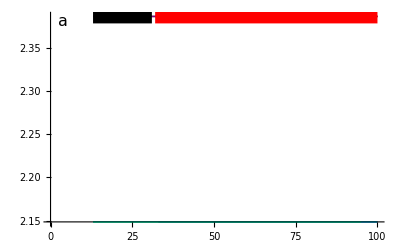
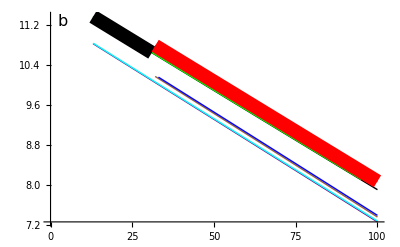
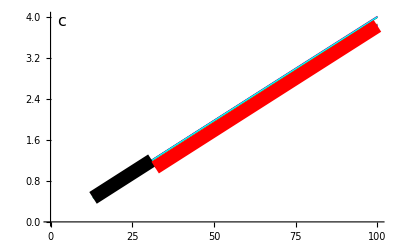
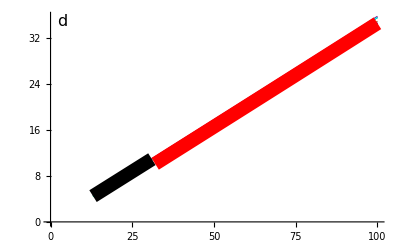
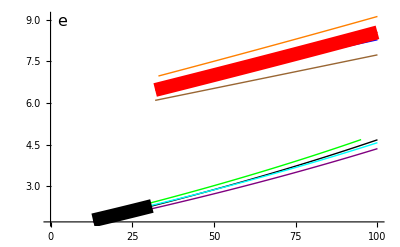
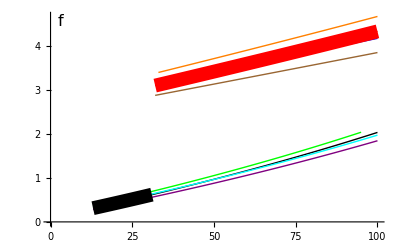
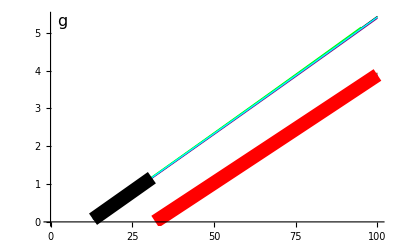
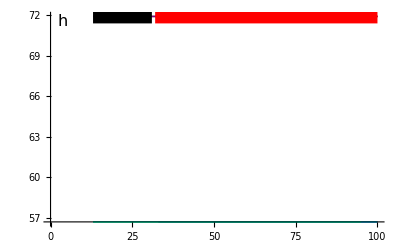
-Graphics-Plant ("P"_"N") | -Graphics-Microbes ("M"_"N") | -Graphics-Detritus N ("D"_"N")
-Graphics-Detritus C ("D"_"C") | -Graphics-Inorganic N (N) | -Graphics-Herbivore ("H"_"N")
-Graphics-Microbi-detritivore ("F"_"N") | -Graphics-H Excretion ("W"_"NH") | -Graphics-F Excretion ("W"_"NF")
-Graphics-M Excretion ("W"_"NM")Inorganic N ("I"_"N") | -Graphics-Primary ProductionInorganic N ("I"_"N") | -Graphics-DecompositionInorganic N ("I"_"N")

```mathematica
labeller = {"Plant ("<>ToString[Subscript["P","N"],StandardForm]<>")","Microbes ("<>ToString[Subscript["M","N"],StandardForm]<>")","Detritus N ("<>ToString[Subscript["D","N"],StandardForm]<>")","Detritus C ("<>ToString[Subscript["D","C"],StandardForm]<>")","Inorganic N (N)","Herbivore ("<>ToString[Subscript["H","N"],StandardForm]<>")","Microbi-detritivore ("<>ToString[Subscript["F","N"],StandardForm]<>")","H Excretion ("<>ToString[Subscript["W","NH"],StandardForm]<>")","F Excretion ("<>ToString[Subscript["W","NF"],StandardForm]<>")","M Excretion ("<>ToString[Subscript["W","NM"],StandardForm]<>")","Primary Production", "Decomposition"};

labeller2 = {"","","","","","","","","","Inorganic N ("<>ToString[Subscript["I","N"],StandardForm]<>")","Inorganic N ("<>ToString[Subscript["I","N"],StandardForm]<>")","Inorganic N ("<>ToString[Subscript["I","N"],StandardForm]<>")"};

labeller3 = {"a", "b","c","d","e","f","g","h","i","j","k","l"};

graphicIN=Grid[Partition[Table[Labeled[ListPlot[Partition[Partition[Riffle[Flatten[ConstantArray[Table[i,{i,13,100}],16]],Flatten[{Transpose[output[[All,All,sel]]],Transpose[output2[[All,All,sel]]]}]],2],88],Joined->True,
PlotStyle->{{Black},{Red}, {Orange}, {Brown}, {Blue},{Green},{Purple},{Cyan},{Thickness[0.025],Black},{Thickness[0.025],Red}, {Thickness[0.025],Orange}, {Thickness[0.025],Brown}, {Thickness[0.025],Blue},{Thickness[0.025],Green},{Thickness[0.025],Purple},{Thickness[0.025],Cyan}},Epilog->Inset[Style[labeller3[[sel]],16],Offset[{0,0},Scaled[{0.04,0.99}]],{Left,Top}]],{labeller[[sel]],labeller2[[sel]]},{Left,Bottom},RotateLabel->True, LabelStyle->{FontFamily->"Times"}],{sel,1,12}],3],Spacings->{0,-6}]
```

```mathematica
Export["AppendixS5_FigureS1.pdf",graphicIN,"PDF", ImageSize->1000]
```